```mathematica
names={"std","FFT_dF","DTCWT","matrix","LC"};
Load[prefix_]:=<|ToExpression[StringReplace[FileBaseName[#],{prefix,".json"}->""]]->
Transpose[Import[#]]&/@FileNames["~/Lab/Projects/data/GIAB/"<>prefix<>"*.json"]|>;
```

```mathematica
DC[ds_,index_]:=Module[{k=Sort[Keys[ds]]},
DistributionChart[
<|#->ds[#]⟦index⟧&/@k|>,ImageSize->280,
ChartLabels->k,PlotLabel->names⟦index⟧]]
```

```mathematica
η={{"Brownian","Real regions","Normal dist."}};
δ=Table[{DC[Load["brownian."],i],DC[Load["best."],i],DC[Load["ndist."],i]},{i,1,5}];
```

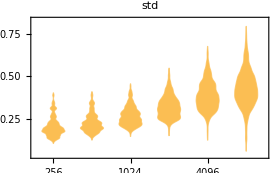
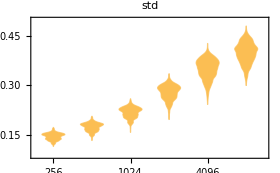
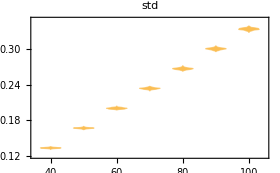
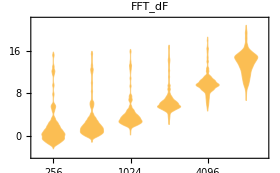
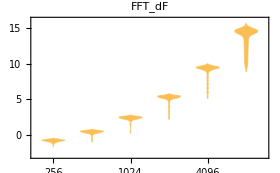
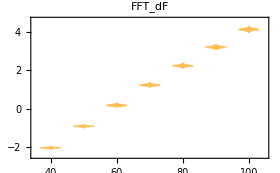
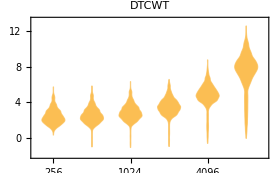
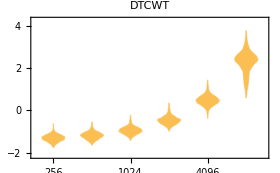
Brownian | Real regions | Normal dist.
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
g=Join[η,δ]//Grid
Export["~/Lab/Projects/data/GIAB/_m.syn.svg",g];
Export["~/Lab/Projects/data/GIAB/_m.syn.jpg",g];
```